```mathematica
FullSimplify[ArcCurvature[{x,f[x]+g[x]},x],{x,f[x],g[x]}∈Reals]
```

√((f''[x]+g''[x])^2/((1+(f'[x]+g'[x])^2)^3))

```mathematica
Grad[f[x,y],{x,y}]
```

{f^(1,0)[x,y],f^(0,1)[x,y]}

```mathematica
Div[f[x,y],{x,y}]
```

Div::sclr: The scalar expression f[x,y] does not have a divergence.

f[x,y]{x,y}

```mathematica
Div[Grad[f[x,y],{x,y}],{x,y}]
```

f^(0,2)[x,y]+f^(2,0)[x,y]

```mathematica
Grad[Sin[x y],{x,y}]
```

{y Cos[x y],x Cos[x y]}

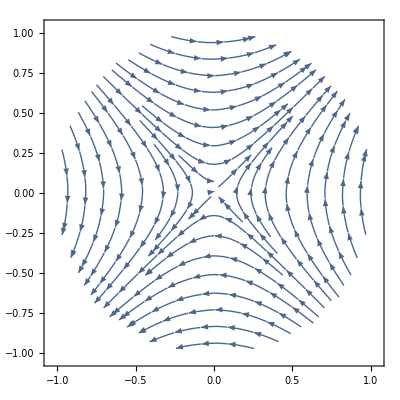

```mathematica
StreamPlot[{y Cos[x y],x Cos[x y]},{x,y}∈Disk[]]
```

```mathematica
Laplacian[Sin[x y],{x,y}]
```

-x^2 Sin[x y]-y^2 Sin[x y]

```mathematica
Plot3D[-x^2 Sin[x y]-y^2 Sin[x y],{x,-102.91902655161662,35.29402630531605},{y,-229.25271694188888,1.8059035874697003}]
```

-Graphics3D-

```mathematica
Plot3D[-x^2 Sin[x y]-y^2 Sin[x y],{x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
x^3-x
```

-x+x^3

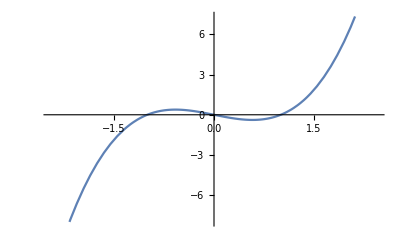

```mathematica
Plot[-x+x^3,{x,-2.449489742783178,2.449489742783178}]
```

```mathematica
FullSimplify[Normalize[{x,x^3-x}].Normalize[{x,a}],{x,a}∈Reals]
```

((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))

```mathematica
lim_(x->-√(1-ⅈ)) ((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))
```

$Aborted

```mathematica
Manipulate[
Plot[{x^3-x,a,((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))},{x,-1,1},PlotRange->{-2,2}]
,{a,-1,1}
]
```

```mathematica
Plot3D[((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4))),{x,a}∈Disk[]]
```

-Graphics3D-

```mathematica
Plot3D[((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4))),{x,-2,2},{a,-1,1}]
```

-Graphics3D-

```mathematica
((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))==1
```

((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))==1

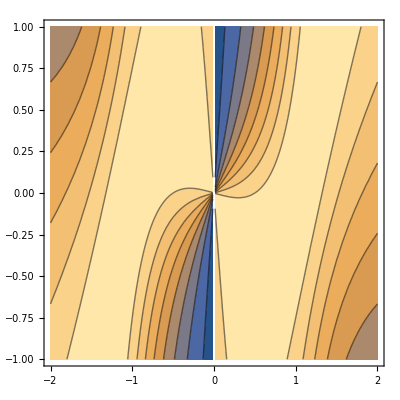

```mathematica
ContourPlot[((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4))),{x,-2,2},{a,-1,1}]
```

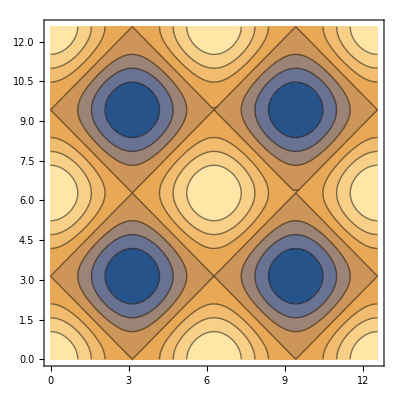

```mathematica
ContourPlot[Cos[x]+Cos[y],{x,0,4Pi},{y,0,4Pi}]
```

```mathematica
ContourPlot[Sin[x y],{x,0,4Pi},{y,0,4Pi}]
```

-Graphics-

```mathematica
ContourPlot[((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))==1,{x,-2,2},{a,-1,1}]
```

-Graphics-

```mathematica
FullSimplify[Normalize[{x,x}].Normalize[{x,a}],{x,a}∈Reals]
```

((a+x) Sign[x])/(√2 √(a^2+x^2))

```mathematica
Manipulate[Plot[((a+x) Sign[x])/(√2 √(a^2+x^2)),{x,-0.9041509852476795,0.9041509852476795}],{a,-0.9041509852476795,0.9041509852476795}]
```

```mathematica
ContourPlot[((a+x) Sign[x])/(√2 √(a^2+x^2))==1,{x,-2,2},{a,-1,1}]
```

-Graphics-

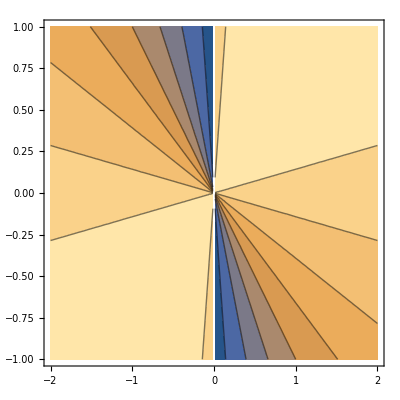

```mathematica
ContourPlot[((a+x) Sign[x])/(√2 √(a^2+x^2)),{x,-2,2},{a,-1,1}]
```

```mathematica
((a+x) Sign[x])/(√2 √(a^2+x^2))
```

```mathematica
Plot3D[((a+x) Sign[x])/(√2 √(a^2+x^2)),{x,-2,2},{a,-1,1}]
```

-Graphics3D-

```mathematica
(a+x) Sign[x]==√2 √(a^2+x^2)
```

(a+x) Sign[x]==√2 √(a^2+x^2)

```mathematica
Reduce[(a+x) Sign[x]==√2 √(a^2+x^2)]
```

$Aborted

```mathematica
(a+x) Sign[x]==√2 √(a^2+x^2)/.a->x
```

2 x Sign[x]==2 √(x^2)

```mathematica
Reduce[2 x Sign[x]==2 √(x^2)]
```

(Re[x]≠0&&Im[x]==0)||x==0

```mathematica
Solve[(a+x) Sign[x]==√2 √(a^2+x^2),a]
```

{{a→(-x Sign[x]^2-2 √(-x^2+x^2 Sign[x]^2))/(-2+Sign[x]^2)},{a→(-x Sign[x]^2+2 √(-x^2+x^2 Sign[x]^2))/(-2+Sign[x]^2)}}

```mathematica
Sign[x]
```

Sign[x]

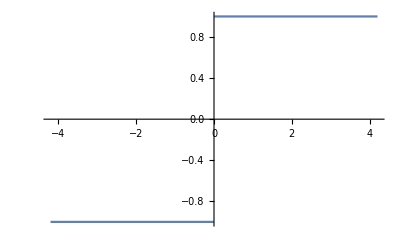

```mathematica
Plot[Sign[x],{x,-4.2,4.2}]
```

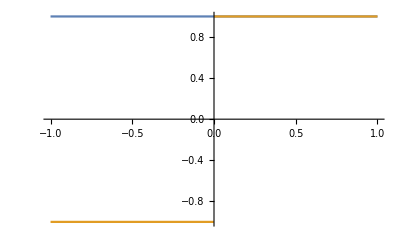

```mathematica
Plot[{Sign[x]^2,Sign[x]},{x,-1,1}]
```

```mathematica
FullSimplify[(-x Sign[x]^2+2 √(-x^2+x^2 Sign[x]^2))/(-2+Sign[x]^2),x∈Reals]
```

x

```mathematica
SymbolName[x]
```

x

```mathematica
FullSimplify[ArcCurvature[{x,x},x],x∈Reals]
```

0

```mathematica
FullSimplify[ArcCurvature[{x,x^a},x],{a,x}∈Reals]
```

√(x^(2+2 a)/((x^2+a^2 x^(2 a))^3)) Abs[-1+a] Abs[a]

```mathematica
Integrate[√(x^(2+2 a)/((x^2+a^2 x^(2 a))^3)) Abs[-1+a] Abs[a],{x,-b,b}]
```

$Aborted

```mathematica
√(x^2+1)-√1
```

-1+√(1+x^2)

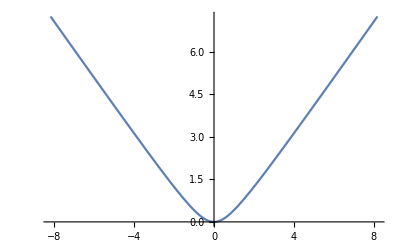

```mathematica
Plot[-1+√(1+x^2),{x,-8.19,8.19}]
```

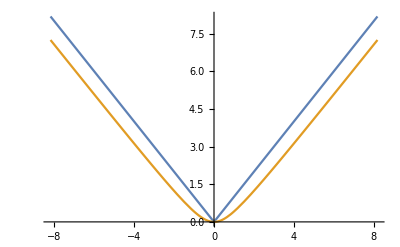

```mathematica
Plot[{Abs[x],-1+√(1+x^2)},{x,-8.19,8.19}]
```

```mathematica
D[{Abs[x],-1+√(1+x^2)},x]
```

{Abs'[x],x/(√(1+x^2))}

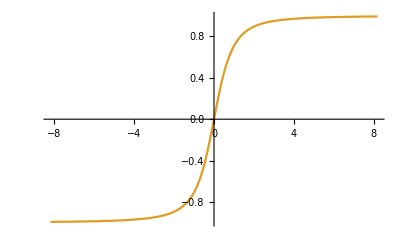

```mathematica
Plot[{Abs'[x],x/(√(1+x^2))},{x,-8.19,8.19}]
```

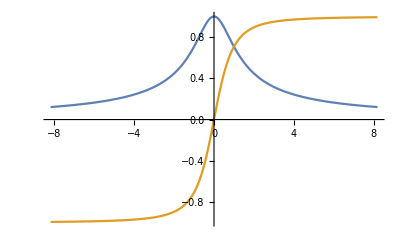

```mathematica
Plot[{1/(√(1+x^2)),x/(√(1+x^2))},{x,-8.19,8.19}]
```

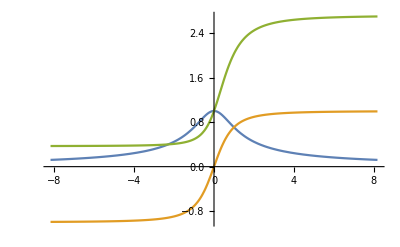

```mathematica
Plot[{1/(√(1+x^2)),x/(√(1+x^2)),Exp[x/(√(1+x^2))]},{x,-8.19,8.19}]
```

```mathematica
x y^2+x-2==0
```

-2+x+x y^2==0

```mathematica
ContourPlot[-2+x+x y^2==0,{x,y}∈Disk[]]
```

-Graphics-

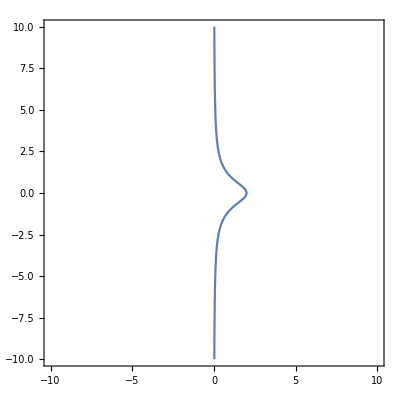

```mathematica
ContourPlot[-2+x+x y^2==0,{x,-10,10},{y,-10,10}]
```

```mathematica
-2+x+x y^2
```

-2+x+x y^2

```mathematica
Plot3D[-2+x+x y^2,{x,-4.666666666666667,4.666666666666667},{y,-2.2882456112707374,2.2882456112707374}]
```

-Graphics3D-

```mathematica
Integrate[FullSimplify[ArcCurvature[{x,x^1},x],{a,x}∈Reals],{x,-∞,∞}]
```

0

```mathematica
Integrate[FullSimplify[ArcCurvature[{x,x^2},x],{a,x}∈Reals],{x,-∞,∞}]
```

2

```mathematica
Integrate[FullSimplify[ArcCurvature[{x,x^3},x],{a,x}∈Reals],{x,-∞,∞}]
```

2

```mathematica
Integrate[FullSimplify[ArcCurvature[{x,x^4},x],{a,x}∈Reals],{x,-∞,∞}]
```

2

```mathematica
Integrate[FullSimplify[ArcCurvature[{x,x^3-x},x],x∈Reals],{x,-∞,∞}]
```

2+√2

```mathematica
N[2+√2]
```

3.41421

```mathematica
FullSimplify[ArcCurvature[{x,α x^3+β x},x],{α,β,x}∈Reals]
```

(6 Abs[x] Abs[α])/((1+(3 x^2 α+β)^2)^(3/2))

```mathematica
FindMaximum[(6 Abs[x] Abs[α])/((1+(3 x^2 α+β)^2)^(3/2)),α]
```

FindMaximum::nrnum: The function value -(6. Abs[x])/((1+(3. x^2+β)^2)^(3/2)) is not a real number at {α} = {1.}.

FindMaximum[(6 Abs[x] Abs[α])/((1+(3 x^2 α+β)^2)^(3/2)),α]

```mathematica
FindMaximum[(6 Abs[x] Abs[α])/((1+(3 x^2 α+β)^2)^(3/2)),{α,1}]
```

FindMaximum::nrnum: The function value -(6. Abs[x])/((1+(3. x^2+β)^2)^(3/2)) is not a real number at {α} = {1.}.

FindMaximum[(6 Abs[x] Abs[α])/((1+(3 x^2 α+β)^2)^(3/2)),{α,1}]

```mathematica
FindMaximum[(6 Abs[x] Abs[α])/((1+(3 x^2 α+β)^2)^(3/2)),{α,1},{x,1},{β,1}]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{413997.,{α→-64175.5,x→-1.07548,β→222689.}}

```mathematica
Manipulate[
Plot[(6 Abs[x] Abs[α])/((1+(3 x^2 α+β)^2)^(3/2)),{x,-2,2}]
,{α,-100,100},{β,-100,100}
]
```

```mathematica
Laplacian[Sin[x y],{x,y}]==0
```

-x^2 Sin[x y]-y^2 Sin[x y]==0

```mathematica
Reduce[-x^2 Sin[x y]-y^2 Sin[x y]==0]
```

(C[1]∈ℤ&&((x≠0&&(y==(2 π C[1])/x||y==(π+2 π C[1])/x))||x==0))||x==-ⅈ y||x==ⅈ y

```mathematica
Reduce[-x^2 Sin[x y]-y^2 Sin[x y]==0,{x,y},Reals]
```

(C[1]∈ℤ&&((x≠0&&(y==(2 π C[1])/x||y==(π+2 π C[1])/x))||x==0))||(x==0&&y==0)

```mathematica
Solve[-x^2 Sin[x y]-y^2 Sin[x y]==0,{x,y},Reals]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→ConditionalExpression[0,C[1]∈ℤ]},{y→ConditionalExpression[(2 π C[1])/x,C[1]∈ℤ]},{y→ConditionalExpression[(π+2 π C[1])/x,C[1]∈ℤ]},{x→0,y→0}}

```mathematica
Laplacian[Sin[x y],{x,y}]
```

-x^2 Sin[x y]-y^2 Sin[x y]

```mathematica
Plot3D[-x^2 Sin[x y]-y^2 Sin[x y],{x,-102.91902655161662,35.29402630531605},{y,-229.25271694188888,1.8059035874697003}]
```

-Graphics3D-

```mathematica
Plot3D[-x^2 Sin[x y]-y^2 Sin[x y],{x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
Plot3D[{Sin[x y],-x^2 Sin[x y]-y^2 Sin[x y]},{x,y}∈Disk[]]
```

-Graphics3D-

Show::gcomb: Could not combine the graphics objects in Show[{ }].

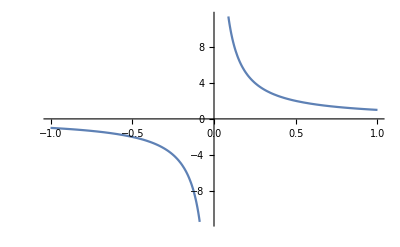
Show[{-Graphics- -Graphics3D-}]

```mathematica
Show[{
Plot3D[{Sin[x y],-x^2 Sin[x y]-y^2 Sin[x y]},{x,y}∈Disk[]]
Plot[1/x,{x,-1,1}]
}]
```

```mathematica
Plot3D[{1/x,Sin[x y],-x^2 Sin[x y]-y^2 Sin[x y]},{x,y}∈Disk[]]
```

-Graphics3D-

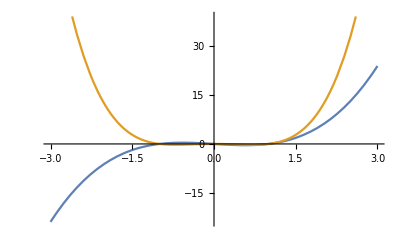

```mathematica
Plot[{x^3-x,x(x^3-x)},{x,-3,3}]
```

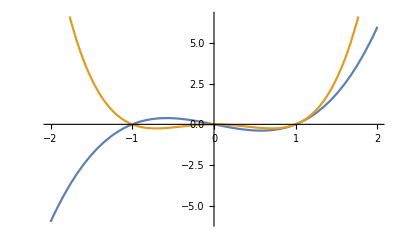

```mathematica
Plot[{x^3-x,x(x^3-x)},{x,-2,2}]
```

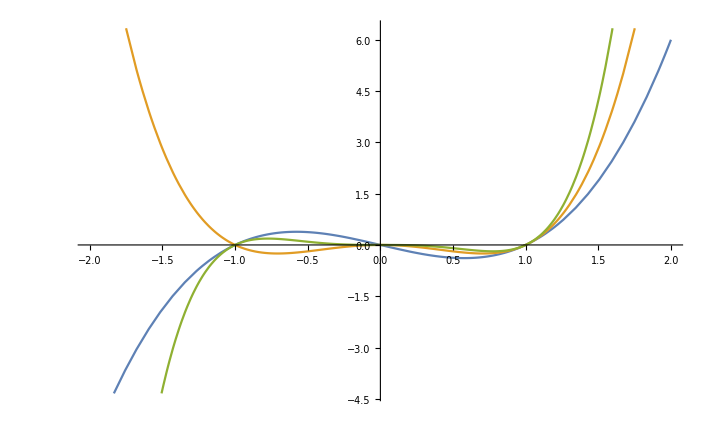

```mathematica
Plot[{x^3-x,x(x^3-x),x^2(x^3-x)},{x,-2,2}]
```